```mathematica
Clear[f,x,w]
```

```mathematica
(*Modulo two pattern fractal the same: Bombieri pattern: odd-even*)
```

```mathematica
p={-1-3 x+x^3,1-x-4*x+x^3 ,1-x-2*x^2+x^3,-1-4 x-x^2+x^3,1-2*x-3*x^2+x^3(*,-1-5 x-2 x^2+x^3*),1-3 x-4 x^2+x^3,1-2*x-5*x^2+x^3}
```

{-1-3 x+x^3,1-5 x+x^3,1-x-2 x^2+x^3,-1-4 x-x^2+x^3,1-2 x-3 x^2+x^3,1-3 x-4 x^2+x^3,1-2 x-5 x^2+x^3}

```mathematica
Table[x/.NSolve[p[[i]]==0,x],{i,Length[p]}]
```

{{-1.53209,-0.347296,1.87939},{-2.33006,0.20164,2.12842},{-0.801938,0.554958,2.24698},{-1.3772,-0.273891,2.65109},{-0.834243,0.34338,3.49086},{-0.857624,0.25324,4.60438},{-0.634609,0.295117,5.33949}}

```mathematica
w=Table[x/.NSolve[p[[i]]==0,x][[3]],{i,Length[p]}]
```

{1.87939,2.12842,2.24698,2.65109,3.49086,4.60438,5.33949}

```mathematica
f[x_]=Fit[w,{1,x},x]
```

0.823497+0.592005 x

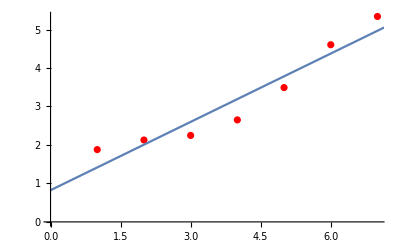

```mathematica
Show[ListPlot[w,PlotStyle->Red],Plot[f[x],{x,0,9}]]
```